```mathematica
SetDirectory["/home/leonard/Documents/ProjectData/PhysicalDistance/kickedRotorIDXP/k_0.9m_30_xp"];
```

```mathematica
pos = Import["./pos.dat","Table"];
inds=Import["./inds.dat","Table"];
refs=Import["./refInds.dat","Table"];
posref={2.π-#[[1]],#[[2]]}&/@pos;
```

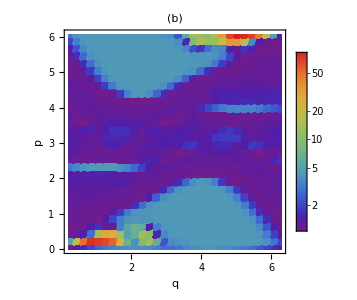

```mathematica
k09=ListDensityPlot[Flatten/@Transpose[{posref,inds}],
{PlotRange->All,
ScalingFunctions->"Log",
ColorFunction->"Rainbow",
Mesh->30,
InterpolationOrder->0,
PlotTheme->"Detailed",
PlotLegends->BarLegend[Automatic,LabelStyle->13],
AspectRatio->1,
PlotLabel->"(b)",
FrameLabel->{"q","p"},
ImageSize->300,
FrameStyle->15,
ImageSize->{Automatic,200}
}]
```

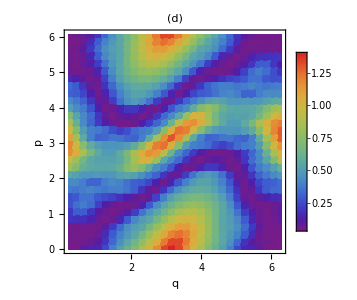

```mathematica
k15=ListDensityPlot[Flatten/@Transpose[{posref,Import["/home/leonard/Documents/ProjectData/PhysicalDistance/kickedRotorIDXP/k_1.5m_30_xp/inds.dat","Table"]}],
{PlotRange->All,
ColorFunction->"Rainbow",
Mesh->30,
InterpolationOrder->0,
PlotTheme->"Detailed",
PlotLegends->BarLegend[Automatic,LabelStyle->13],
AspectRatio->1,
PlotLabel->"(d)",
FrameLabel->{"q","p"},
ImageSize->300,
FrameStyle->15,
ImageSize->{Automatic,200}
}]
```

```mathematica
k09c=Import["/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/fig5c.png","Image"];
k15c=Import["/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/fig6c.png","Image"];
```

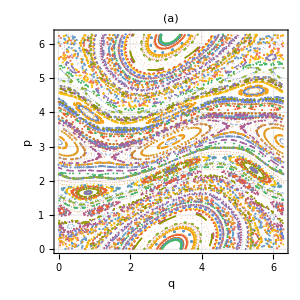
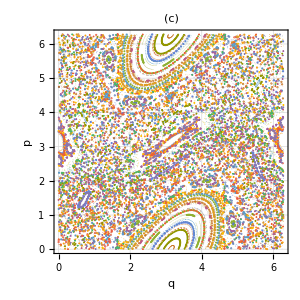
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{k09c,k09},{k15c,k15}}]
```

```mathematica
Export["/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/krcm.png",%65]
```

/home/leonard/Documents/Projects/PhysicalDistance/Paper/figs/krcm.png